```mathematica
-----Simple Harmonic Oscillatior----
```

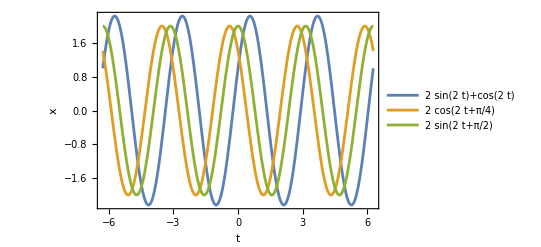

```mathematica
Plot[{2Sin[2 t]+Cos[2 t],2Cos[2 t+ Pi/4],2Sin[2 t + Pi/2]},{t,-2Pi,2Pi},PlotLegends->"Expressions",Frame->True,FrameLabel->{"t","x"}]
```

```mathematica
Manipulate[Plot[A Cos[ω t+ ϕ],{t,-2Pi, 2Pi},Frame->True,PlotRange->{-5,5},PlotLabel->Row[{"A=",A,";ω =",ω, "; ϕ",ϕ}]],{A,1,5,0.1},{ω,0.1,5,0.1},{ϕ,-Pi, Pi, Pi/16}]
```

```mathematica
-----Non-dimensionlisation: Simple Pendulum-----
```

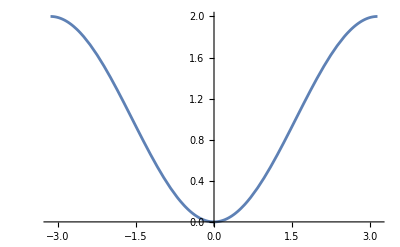

```mathematica
Plot[1-Cos[Θ],{Θ,-Pi,Pi}]
```

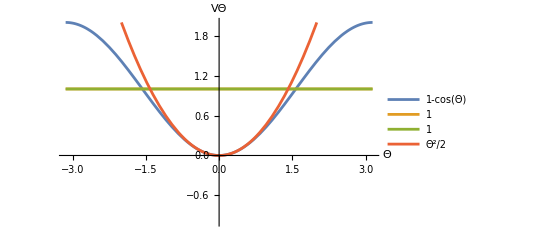

```mathematica
Plot[{1-Cos[Θ],1,1,Θ^2/2},{Θ,-Pi,Pi},PlotRange->{-1,2},AxesLabel->{Style[Θ,16],Style[VΘ,16]},AxesStyle->Thick,PlotLegends->"Expressions"]
```

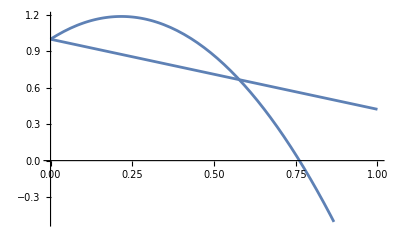

```mathematica
Plot[{-γ/Cos[Θ]^2 x^2 + Tan[Θ] x +1,-Tan[ϕ] x +1}/.{Θ->Pi/3,ϕ->Pi/6, γ->1},{x,0,1}]
```

```mathematica
Manipulate[Plot[{-γ/Cos[Θ]^2 x^2 + Tan[Θ] x +1,-Tan[ϕ] x +1},{x,0,10}],{Θ,0,Pi/2},{ϕ,0,Pi/2},{γ,0,1}]
```

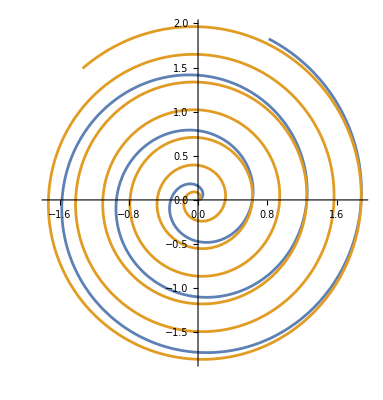

```mathematica
ParametricPlot[{{0.1 t Cos[t],0.1 t Sin[t]},{0.1 t Cos[2 t],0.1 t Sin[2 t]}},{t,0,20}]
```

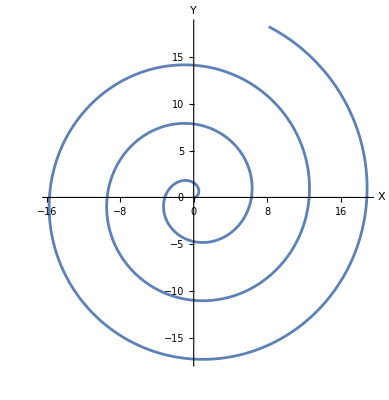

```mathematica
ParametricPlot[{T Cos[T], T Sin[T]},{T,0,20},AxesLabel->{"X","Y"}]
```

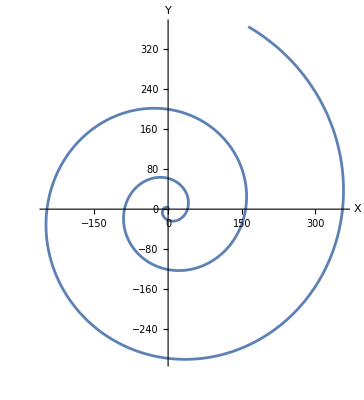

```mathematica
ParametricPlot[{T^2 Cos[T], T^2 Sin[T]},{T,0,20},AxesLabel->{"X","Y"}]
```

```mathematica
---------Charge and Current in LC circuit--------
```

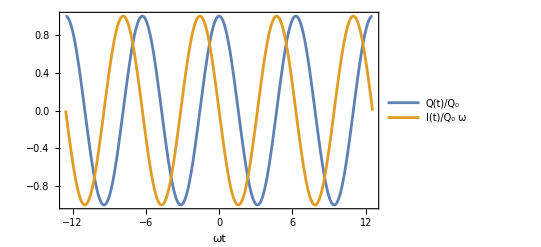

```mathematica
Plot[{Cos[t],-Sin[t]},{t,-4 Pi,4 Pi},Frame->True,PlotLegends->{"Q(t)/Q_0","I(t)/Q_0 ω"},FrameLabel->{"ωt",""}]
```

```mathematica
-------------------Learning some calculus tools (Integration, Differentiation, Solving Differential Equation)------------
```

```mathematica
------Derivative-------
```

```mathematica
D[Log[x],x]
```

1/x

```mathematica
D[x Log[x],x]
```

1+Log[x]

```mathematica
D[Log[x]/x,x]
```

1/x^2-Log[x]/x^2

```mathematica
---Find where log x/x has extrema exactly. First plot and check and then solve [d/dx=0]-----
```

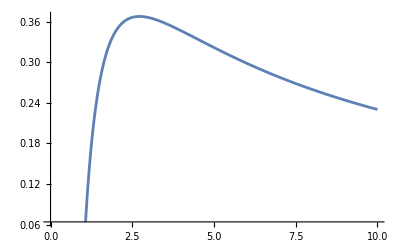

```mathematica
Plot[Log[x]/x,{x,0,10}]
```

```mathematica
Solve[D[Log[x]/x,x]==0,x]
```

{{x→ⅇ}}

```mathematica
Solve[D[Log[x]/x,x]==0,x]//N
```

{{x→2.71828}}

```mathematica
Solve[2 x^2+2 x -1 ==0,x]
```

{{x→1/2 (-1-√3)},{x→1/2 (-1+√3)}}

```mathematica
sol = Solve[2 x^2+2x-1==0,x]
```

{{x→1/2 (-1-√3)},{x→1/2 (-1+√3)}}

```mathematica
sol[[1]]
```

{x→1/2 (-1-√3)}

```mathematica
x/.sol[[1]]
```

1/2 (-1-√3)

```mathematica
2 x^2+2x-1/.sol[[1]]//N
```

0.

```mathematica
---------Second Derivative-----
```

```mathematica
D[Log[x],{x,2}]
```

-1/x^2

```mathematica
-----Third Derivative----
```

```mathematica
D[Log[x],{x,3}]
```

2/x^3

```mathematica
D[Log[x y]/x,x]
```

1/x^2-Log[x y]/x^2

```mathematica
------Analytical Integration----
```

```mathematica
Integrate[Log[x]/x,x]
```

Log[x]^2/2

```mathematica
Integrate[Log[x]/x,{x,1,2}]
```

Log[2]^2/2

```mathematica
Integrate[Log[x y]/x,x]
```

1/2 Log[x y]^2

```mathematica
Integrate[Log[x y]/x,x,y]
```

1/2 y (-2 Log[x]+Log[x y]^2)

```mathematica
Integrate[Log[x y]/x,{x,1,2},{y,1,2}]
```

1/2 Log[2] (-2+Log[32])

```mathematica
------Numerical Integration----
```

```mathematica
Integrate[1/(√(1+t+t^2)),{t,0,1}]//N
```

0.767652

```mathematica
NIntegrate[1/(√(1+t+t^2)),{t,0,1}]//N
```

0.767652

```mathematica
NIntegrate[1/(√(1+a t+t^2)),{t,0,1}]//N
```

NIntegrate::inumr: The integrand 1/(√(1+a t+t^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand 1./(√(1.+a t+t^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[1./(√(1.+a t+t^2)),{t,0.,1.}]

```mathematica
f[a_]:=NIntegrate[1/(√(1+a t+t^2)),{t,0,1}]//N
```

```mathematica
f[1]
```

0.767652

```mathematica
f[3]
```

0.638917

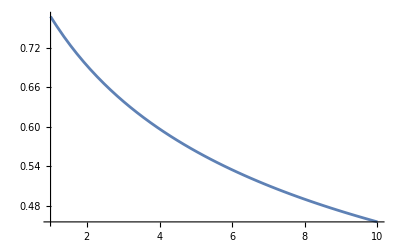

```mathematica
Plot[f[a],{a,1,10}]
```

```mathematica
------Solving Differential Equations------
```

```mathematica
DSolve[x'[t]==-2x[t],x[t],t]
```

{{x[t]→ⅇ^(-2 t) C[1]}}

```mathematica
DSolve[{x'[t]==-2x[t],x[0]==1},x[t],t]
```

{{x[t]→ⅇ^(-2 t)}}

```mathematica
------- Solving coupled differential equation---
```

```mathematica
DSolve[{x'[t]==-y[t],y'[t]==-x[t]},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
dsol = DSolve[{x'[t]==-y[t],y'[t]==-x[t]},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
x[t]/.dsol[[1]]
```

1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2]

```mathematica
dsol = DSolve[{x'[t]==-y[t],y'[t]==-x[t],x[0]==2,y[0]==1},{x[t],y[t]},t]
```

{{x[t]→1/2 ⅇ^-t (3+ⅇ^(2 t)),y[t]→-1/2 ⅇ^-t (-3+ⅇ^(2 t))}}

```mathematica
X[t_]=x[t]/.dsol[[1]]
```

1/2 ⅇ^-t (3+ⅇ^(2 t))

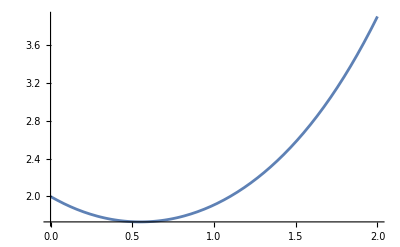

```mathematica
Plot[X[t],{t,0,2}]
```

```mathematica
Y[t_]=y[t]/.dsol[[1]]
```

-1/2 ⅇ^-t (-3+ⅇ^(2 t))

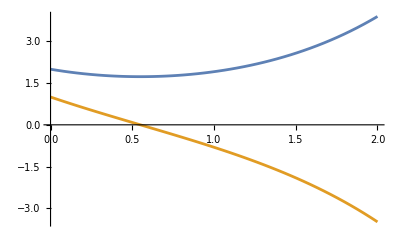

```mathematica
Plot[{X[t],Y[t]},{t,0,2}]
```

```mathematica
DSolve[x''[t]==-x[t],x[t],t]
```

{{x[t]→C[1] Cos[t]+C[2] Sin[t]}}

```mathematica
DSolve[x''[t]==-x[t]-x'[t],x[t],t]
```

{{x[t]→ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]}}

```mathematica
DSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

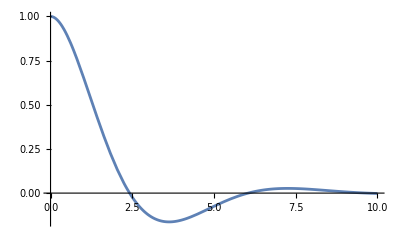

```mathematica
Plot[x[t]/.dsol[[1]],{t,0,10},PlotRange->All]
```

```mathematica
dsol=NDSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
X[t_]=x[t]/.dsol[[1]]
```

InterpolatingFunction[…][t]

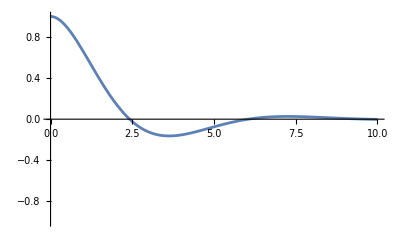

```mathematica
Plot[X[t],{t,0,10},PlotRange->{-1,1}]
```

```mathematica
dsol = NDSolve[{x''[t]==-x[t]-0.5  x'[t],x[0]==1,x'[0]==0},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
X[t_]=x[t]/.dsol[[1]]
```

InterpolatingFunction[…][t]

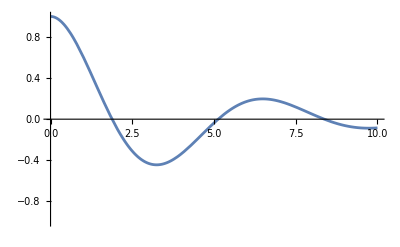

```mathematica
Plot[X[t],{t,0,10},PlotRange->{-1,1}]
```

```mathematica
DSolve[x''[t]==-x[t]-0.5  x'[t] x[t]^2,x[t],t]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

DSolve[x''[t]==-x[t]-0.5 x[t]^2 x'[t],x[t],t]

```mathematica
dsol = NDSolve[{x''[t]==-x[t]- 0.5 x'[t] x[t]^2,x[0]==1,x'[0]==0},x[t],{t,0,10}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {-π^2 Cos[4.64193+π t]==-Cos[4.64193+π t]+1.5708 («1»)^2 Sin[4.64193+π t],True,False}.

NDSolve[{-π^2 Cos[4.64193+π t]==-Cos[4.64193+π t]+1.5708 Cos[4.64193+π t]^2 Sin[4.64193+π t],True,False},Cos[4.64193+π t],{t,0,10}]

```mathematica
X[t_]=x[t]/.dsol[[1]]
```

InterpolatingFunction[…][t]

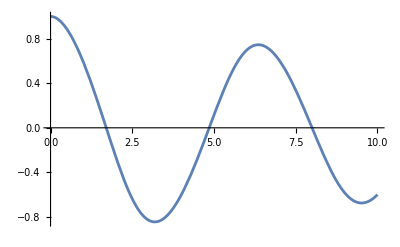

```mathematica
Plot[X[t],{t,0,10}]
```

```mathematica
---Solving damped LCR circuit initial value problem-----
```

```mathematica
ClearAll["`*"]
```

```mathematica
DSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {-π^2 Cos[4.64193+π t]==-Cos[4.64193+π t]+π Sin[4.64193+π t],True,False}.

DSolve[{-π^2 Cos[4.64193+π t]==-Cos[4.64193+π t]+π Sin[4.64193+π t],True,False},Cos[4.64193+π t],t]

```mathematica
DSolve[{x''[t]==-γ x'[t]-x[t],x[0]=1,x'[0]=0},x[t],t]
```

DSolve::deqn: Equation or list of equations expected instead of 1 in the first argument {x''[t]==-x[t]-γ x'[t],1,0}.

DSolve[{x''[t]==-x[t]-γ x'[t],1,0},x[t],t]

```mathematica
f[γ_]:=DSolve[{x''[t]==-γ x'[t]-x[t],x[0]=1,x'[0]=0},x[t],t]
```

```mathematica
f[2]
```

DSolve::deqn: Equation or list of equations expected instead of 1 in the first argument {x''[t]==-x[t]-2 x'[t],1,0}.

DSolve[{x''[t]==-x[t]-2 x'[t],1,0},x[t],t]

```mathematica
q[t_]= A Exp[-α  t]Cos[β  t + ϕ]
```

A ⅇ^(-t α) Cos[t β+ϕ]

```mathematica
first = D[q[t],t]
```

-A ⅇ^(-t α) α Cos[t β+ϕ]-A ⅇ^(-t α) β Sin[t β+ϕ]

```mathematica
second=D[q[t],{t,2}]
```

A ⅇ^(-t α) α^2 Cos[t β+ϕ]-A ⅇ^(-t α) β^2 Cos[t β+ϕ]+2 A ⅇ^(-t α) α β Sin[t β+ϕ]

```mathematica
second== -γ q[t]-first
```

A ⅇ^(-t α) α^2 Cos[t β+ϕ]-A ⅇ^(-t α) β^2 Cos[t β+ϕ]+2 A ⅇ^(-t α) α β Sin[t β+ϕ]==A ⅇ^(-t α) α Cos[t β+ϕ]-A ⅇ^(-t α) γ Cos[t β+ϕ]+A ⅇ^(-t α) β Sin[t β+ϕ]

```mathematica
equation = second - (-γ q[t]-first)
```

-A ⅇ^(-t α) α Cos[t β+ϕ]+A ⅇ^(-t α) α^2 Cos[t β+ϕ]-A ⅇ^(-t α) β^2 Cos[t β+ϕ]+A ⅇ^(-t α) γ Cos[t β+ϕ]-A ⅇ^(-t α) β Sin[t β+ϕ]+2 A ⅇ^(-t α) α β Sin[t β+ϕ]

```mathematica
coeffcos = Coefficient[equation, Cos[β t + ϕ]]/(A Exp[-α t])//Simplify
```

-α+α^2-β^2+γ

```mathematica
coeffsin = Coefficient[equation, Sin[β t + ϕ]]/(A Exp[-α t])//Simplify
```

(-1+2 α) β

```mathematica
Solve[{coeffcos==0,coeffsin==0},{α,β}]
```

{{α→1/2,β→-1/2 √(-1+4 γ)},{α→1/2,β→1/2 √(-1+4 γ)},{α→1/2 (1-√(1-4 γ)),β→0},{α→1/2 (1+√(1-4 γ)),β→0}}

```mathematica
sol=Solve[{coeffcos==0,coeffsin==0},{α,β}]
```

{{α→1/2,β→-1/2 √(-1+4 γ)},{α→1/2,β→1/2 √(-1+4 γ)},{α→1/2 (1-√(1-4 γ)),β→0},{α→1/2 (1+√(1-4 γ)),β→0}}

```mathematica
sol[[2]]
```

{α→1/2,β→1/2 √(-1+4 γ)}

```mathematica
qsol[t_]=q[t]/.sol[[2]]
```

A ⅇ^(-t/2) Cos[1/2 t √(-1+4 γ)+ϕ]

```mathematica
qsol[0]==1
```

A Cos[ϕ]==1

```mathematica
(D[qsol[t],t]/.t->0)==0
```

-1/2 A Cos[ϕ]-1/2 A √(-1+4 γ) Sin[ϕ]==0

```mathematica
bcsol=Solve[{qsol[0]==1,(D[qsol[t],t]/.t->0)==0},{A,ϕ}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{A→-(2 √γ)/(√(-1+4 γ)),ϕ→-ArcCos[-(√(-1+4 γ))/(2 √γ)]},{A→-(2 √γ)/(√(-1+4 γ)),ϕ→ArcCos[-(√(-1+4 γ))/(2 √γ)]},{A→(2 √γ)/(√(-1+4 γ)),ϕ→-ArcCos[(√(-1+4 γ))/(2 √γ)]},{A→(2 √γ)/(√(-1+4 γ)),ϕ→ArcCos[(√(-1+4 γ))/(2 √γ)]}}

```mathematica
bcsol[[3]]
```

{A→(2 √γ)/(√(-1+4 γ)),ϕ→-ArcCos[(√(-1+4 γ))/(2 √γ)]}

```mathematica
qfinal[t_]=qsol[t]/.bcsol[[3]]
```

(2 ⅇ^(-t/2) √γ Cos[1/2 t √(-1+4 γ)-ArcCos[(√(-1+4 γ))/(2 √γ)]])/(√(-1+4 γ))

```mathematica
qfinal[t_]=qsol[t]/.bcsol[[3]]/.γ->2
```

2 √(2/7) ⅇ^(-t/2) Cos[(√7 t)/2-ArcCos[(√(7/2))/2]]

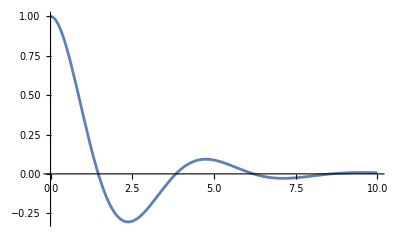

```mathematica
Plot[qfinal[t],{t,0,10},PlotRange->All]
```

```mathematica
qfinal[γ_,t_]=qsol[t]/.bcsol[[3]]
```

(2 ⅇ^(-t/2) √γ Cos[1/2 t √(-1+4 γ)-ArcCos[(√(-1+4 γ))/(2 √γ)]])/(√(-1+4 γ))

```mathematica
Manipulate[Plot[qfinal[γ,t],{t,0,10},PlotRange->All],{γ,0.26,2}]
```